# Contouring a multi-valued function on a triangulated grid (2D/3D)

## Tao Ju (Dec 2020)

## Code

### 2D

Given an input triangulated mesh (points and triangles) with a vector of material values at each point, this code performs Dual Contouring to extract the interface between different materials. The output is:
- a list of vertices and line segments, and two material indices per segment. [Contour curve]
- a list of vertices and triangles, and one material for each triangle [Solid fill]

```mathematica
contourTriMultiDC[pts_,tris_,vals_]:=Module[{ptMats,nmat=Length[vals⟦1⟧],verts,segs,segMats,edgeHash,edges,edgeFaces,edgePtInds,npts=Length[pts],ntris=Length[tris],edgeMap={{1,2},{2,3},{3,1}},ind,edgePoints,triVertInds,newseg,ct,ct2,ct3,bdVertInd,fillVerts,fillTris,fillMats,seg},
(* get material index at each point *)
ptMats=Map[getMaxPos,vals];

(* create adj table from edges to faces *)
edgeHash[_,_]=0;
edges=Table[{},{ntris*3}];
edgeFaces=Table[{},{ntris*3}];
ct=0;
Do[If[(ind=edgeHash[tris⟦i,edgeMap⟦j,1⟧⟧,tris⟦i,edgeMap⟦j,2⟧⟧])==0,
ct+=1;
edges⟦ct⟧=tris⟦i,edgeMap⟦j⟧⟧;
edgeFaces⟦ct⟧={i};
edgeHash[tris⟦i,edgeMap⟦j,1⟧⟧,tris⟦i,edgeMap⟦j,2⟧⟧]=ct;
edgeHash[tris⟦i,edgeMap⟦j,2⟧⟧,tris⟦i,edgeMap⟦j,1⟧⟧]=ct,
AppendTo[edgeFaces⟦ind⟧,i]],
{i,ntris},{j,3}];
edges=edges⟦1;;ct⟧;
edgeFaces=edgeFaces⟦1;;ct⟧;

(* create interpolation points, one per edge with material change *)
edgePoints=Map[
If[ptMats⟦#⟦1⟧⟧==ptMats⟦#⟦2⟧⟧,
{},
interpEdge2Mat[pts⟦#⟦1⟧⟧,pts⟦#⟦2⟧⟧,vals⟦#⟦1⟧,ptMats⟦#⟧⟧,vals⟦#⟦2⟧,ptMats⟦#⟧⟧]]&,edges];
edgePtInds=Table[0,{Length[edges]}];

(* create vertices, one per triangle with material change *)
verts=Table[{},{ntris*7}];
ct=0;
triVertInds=Map[
If[ptMats⟦#⟦1⟧⟧==ptMats⟦#⟦2⟧⟧==ptMats⟦#⟦3⟧⟧,
0,
ind=#;
ct+=1;
verts⟦ct⟧=getMassPoint[edgePoints⟦Map[edgeHash[ind⟦#⟦1⟧⟧,ind⟦#⟦2⟧⟧]&,edgeMap]⟧];
ct]&,
tris];

(* create segments *)
segs=Table[{},{Length[edges]}];
segMats=Table[{},{Length[edges]}];
ct2=0;
Do[
If[ptMats⟦edges⟦i,1⟧⟧≠ptMats⟦edges⟦i,2⟧⟧,
ct2+=1;
segMats⟦ct2⟧=ptMats⟦edges⟦i⟧⟧;
If[Length[edgeFaces⟦i⟧]==1,
(* boundary edge: connect edge point and triangle point *)
ct+=1;
verts⟦ct⟧=edgePoints⟦i⟧;
edgePtInds⟦i⟧=ct;
newseg={triVertInds⟦edgeFaces⟦i,1⟧⟧,ct},
(* interior edge: connect two triangle points *)
newseg=triVertInds⟦edgeFaces⟦i⟧⟧];
If[orientation[pts⟦edges⟦i,1⟧⟧-pts⟦edges⟦i,2⟧⟧,verts⟦newseg⟦1⟧⟧-pts⟦edges⟦i,1⟧⟧]<0,
newseg=Reverse[newseg]];
segs⟦ct2⟧=newseg],
{i,Length[edges]}];

verts=verts⟦1;;ct⟧;
segs=segs⟦1;;ct2⟧;
segMats=segMats⟦1;;ct2⟧;

(* create fill triangles *)
fillVerts=Join[verts,pts];
fillTris=Table[{},{ntris*6}];
fillMats=Table[0,{ntris*6}];
ct3=0;

(* first type of triangles: dual to mesh edges with a material change *)
Do[
If[ptMats⟦edges⟦i,1⟧⟧≠ptMats⟦edges⟦i,2⟧⟧,
If[Length[edgeFaces⟦i⟧]==1,
(* boundary edge: connect edge point and triangle point *)
seg={triVertInds⟦edgeFaces⟦i,1⟧⟧,edgePtInds⟦i⟧},
(* interior edge: connect two triangle points *)
seg=triVertInds⟦edgeFaces⟦i⟧⟧];
ct3+=1;
fillTris⟦ct3⟧=Append[seg,ct+edges⟦i,1⟧];
fillMats⟦ct3⟧=ptMats⟦edges⟦i,1⟧⟧;
ct3+=1;
fillTris⟦ct3⟧=Append[seg,ct+edges⟦i,2⟧];
fillMats⟦ct3⟧=ptMats⟦edges⟦i,2⟧⟧],
{i,Length[edges]}];

(* second type of triangles: original mesh triangle, if there is no material change, or a third of the triangle, if there is some edge with no material change *)
Do[If[ptMats⟦tris⟦i,1⟧⟧==ptMats⟦tris⟦i,2⟧⟧==ptMats⟦tris⟦i,3⟧⟧,
ct3+=1;
fillTris⟦ct3⟧=tris⟦i⟧+{ct,ct,ct};
fillMats⟦ct3⟧=ptMats⟦tris⟦i,1⟧⟧,
Do[If[ptMats⟦tris⟦i,edgeMap⟦j,1⟧⟧⟧==ptMats⟦tris⟦i,edgeMap⟦j,2⟧⟧⟧,
ct3+=1;
fillTris⟦ct3⟧=Append[tris⟦i,edgeMap⟦j⟧⟧+{ct,ct},triVertInds⟦i⟧];
fillMats⟦ct3⟧=ptMats⟦tris⟦i,edgeMap⟦j,1⟧⟧⟧],
{j,3}]],
{i,Length[tris]}];

(* Print[ct3,fillVerts,fillTris,fillMats]; *)
fillTris=fillTris⟦1;;ct3⟧;
fillMats=fillMats⟦1;;ct3⟧;

{verts,segs,segMats,fillVerts,fillTris,fillMats}
];
```

Check if two 2D vectors u,v are turning left (ccw):

```mathematica
orientation[u_,v_]:=Sign[Cross[Append[u,0],Append[v,0]]⟦3⟧];
```

A different contouring method: it connects face vertices to edge vertices. The number of segments would approximately double, but it ensures that all segments stay within each triangle. This method, however, tends to generate more jagged contours.

```mathematica
contourTriMultiDCRefined[pts_,tris_,vals_]:=Module[{ptMats,nmat=Length[vals⟦1⟧],verts,segs,segMats,edgeHash,edges,edgeFaces,npts=Length[pts],ntris=Length[tris],edgeMap={{1,2},{2,3},{3,1}},ind,edgeVertInds,triVertInds,einds},
(* get material index at each point *)
ptMats=Map[getMaxPos,vals];

(* create adj table from edges to faces *)
edgeHash[_,_]=0;
edges={};
edgeFaces={};
Do[If[(ind=edgeHash[tris⟦i,edgeMap⟦j,1⟧⟧,tris⟦i,edgeMap⟦j,2⟧⟧])==0,
AppendTo[edges,tris⟦i,edgeMap⟦j⟧⟧];
AppendTo[edgeFaces,{i}];
edgeHash[tris⟦i,edgeMap⟦j,1⟧⟧,tris⟦i,edgeMap⟦j,2⟧⟧]=Length[edges];
edgeHash[tris⟦i,edgeMap⟦j,2⟧⟧,tris⟦i,edgeMap⟦j,1⟧⟧]=Length[edges],
AppendTo[edgeFaces⟦ind⟧,i]],
{i,ntris},{j,3}];

(* create interpolation points, one per edge with material change *)
verts={};
edgeVertInds=Map[
If[ptMats⟦#⟦1⟧⟧==ptMats⟦#⟦2⟧⟧,
0,
AppendTo[verts,interpEdge2Mat[pts⟦#⟦1⟧⟧,pts⟦#⟦2⟧⟧,vals⟦#⟦1⟧,ptMats⟦#⟧⟧,vals⟦#⟦2⟧,ptMats⟦#⟧⟧]];
Length[verts]]&,edges];

(* create vertices and segments for each triangle with material change *)
segs={};
segMats={};
Do[
If[!(ptMats⟦tris⟦i,1⟧⟧==ptMats⟦tris⟦i,2⟧⟧==ptMats⟦tris⟦i,3⟧⟧),
(* create face vertex *)
einds=Map[edgeHash[tris⟦i,#⟦1⟧⟧,tris⟦i,#⟦2⟧⟧]&,edgeMap];
AppendTo[verts,Mean[verts⟦Select[edgeVertInds⟦einds⟧,#>0&]⟧]];
(* create segments *)
Do[If[edgeVertInds⟦einds⟦j⟧⟧≠0,
AppendTo[segs,{Length[verts],edgeVertInds⟦einds⟦j⟧⟧}];
AppendTo[segMats,ptMats⟦tris⟦i,edgeMap⟦j⟧⟧⟧]],
{j,3}]],
{i,Length[tris]}];

{verts,segs,segMats}
];
```

Get the index of the material with highest value:

```mathematica
getMaxPos[vals_]:=MaximalBy[Range[Length[vals]],vals⟦#⟧&]⟦1⟧;
```

Compute the centroid of a number points (possibly empty):

```mathematica
getMassPoint[pts_]:=Mean[Select[pts,#≠{}&]];
```

Compute linear interpolation point along edge {p,q} given two values at each point. The order of the two values should be different at p and q.

```mathematica
interpEdge2Mat[p_,q_,pvals_,qvals_]:=Module[{t=Abs[pvals⟦1⟧-pvals⟦2⟧]/(Abs[pvals⟦1⟧-pvals⟦2⟧]+Abs[qvals⟦1⟧-qvals⟦2⟧])},
(1-t)p+t*q];
```

This function extracts the contour for each material, given the output of the functions above, with an additional “shrink” factor to allow visualization of adjacent contours. Shrink is multiplied to the normalized mean curvature vector (inward); 0 means no shrinking.

```mathematica
getContourAllMats2D[verts_,segs_,segmats_,nmat_,shrink_]:=Table[getContourByMat2D[verts,segs,segmats,i,shrink],{i,nmat}];
```

```mathematica
getContourByMat2D[verts_,segs_,segmats_,mat_,shrink_]:=Module[{inds1,inds2,nsegs,nvertInds,nverts,vertUsed,vertNewInds,vertnorms,nm},
(* select segments by mat *)
inds1=Select[Range[Length[segs]],segmats⟦#,1⟧==mat&];
inds2=Select[Range[Length[segs]],segmats⟦#,2⟧==mat&];
nsegs=Join[segs⟦inds1⟧,Map[Reverse,segs⟦inds2⟧]];
(* prune unused vertices *)
vertUsed=Map[False&,verts];
Scan[(vertUsed⟦#⟦1⟧⟧=True;vertUsed⟦#⟦2⟧⟧=True)&,nsegs];
nvertInds=Pick[Range[Length[verts]],vertUsed];
vertNewInds=Map[0&,verts];
Do[vertNewInds⟦nvertInds⟦i⟧⟧=i,{i,Length[nvertInds]}];
nverts=verts⟦nvertInds⟧;
nsegs=Map[vertNewInds⟦#⟧&,nsegs,{2}];
(* shrink *)
vertnorms=Map[{0,0}&,nverts];
Scan[(nm=perp[nverts⟦#⟦2⟧⟧-nverts⟦#⟦1⟧⟧];
vertnorms⟦#⟦1⟧⟧+=nm;
vertnorms⟦#⟦2⟧⟧+=nm)&,nsegs];
nverts+=shrink*Map[Normalize,vertnorms];
{nverts,nsegs}];
```

```mathematica
perp[{x_,y_}]:={-y,x};
```

### 3D

Given an input tet mesh (points and tets) with a vector of material values at each point, this code performs Dual Contouring to extract the interface between different materials. The output is a list of vertices and polygonal facet, and two material indices per facet.

```mathematica
contourTetMultiDC[pts_,tets_,vals_]:=Module[{ptMats,nmat=Length[vals⟦1⟧],verts,segs,segMats,edgeHash,bdfaceHash,edges,edgeTets,npts=Length[pts],ntets=Length[tets],edgeMap={{1,2},{1,3},{1,4},{2,3},{2,4},{3,4}},ind,edgePoints,tetVertInds,ot,ends,tri,ct,ct2,temp,newseg,p1,p2,ps},

(* get material index at each point *)
ptMats=Map[getMaxPos,vals];

(* create adj table from edges to faces *)
edgeHash[_,_]=0;
edges=Table[{},{ntets*6}];
edgeTets=Table[{},{ntets*6}];
ct=0;
temp=Ceiling[ntets/10];
Do[
If[Mod[i,temp]==0&&j==1,Print[PercentForm[N[i/ntets]]]];
If[(ind=edgeHash[tets⟦i,edgeMap⟦j,1⟧⟧,tets⟦i,edgeMap⟦j,2⟧⟧])==0,
ct+=1;
edges⟦ct⟧=tets⟦i,edgeMap⟦j⟧⟧;
edgeTets⟦ct⟧={i};
edgeHash[tets⟦i,edgeMap⟦j,1⟧⟧,tets⟦i,edgeMap⟦j,2⟧⟧]=ct;
edgeHash[tets⟦i,edgeMap⟦j,2⟧⟧,tets⟦i,edgeMap⟦j,1⟧⟧]=ct,
AppendTo[edgeTets⟦ind⟧,i]],
{i,ntets},{j,6}];
edges=edges⟦1;;ct⟧;
edgeTets=edgeTets⟦1;;ct⟧;
Print["Adj table DONE."];

(* create interpolation points, one per edge with material change *)
edgePoints=Map[
If[ptMats⟦#⟦1⟧⟧==ptMats⟦#⟦2⟧⟧,
{},
interpEdge2Mat[pts⟦#⟦1⟧⟧,pts⟦#⟦2⟧⟧,vals⟦#⟦1⟧,ptMats⟦#⟧⟧,vals⟦#⟦2⟧,ptMats⟦#⟧⟧]]&,edges];
Print["Edge points DONE."];

(* create vertices, one per tet with material change *)
verts=Table[{},{ntets*5}];
ct=0;
tetVertInds=Map[
If[ptMats⟦#⟦1⟧⟧==ptMats⟦#⟦2⟧⟧==ptMats⟦#⟦3⟧⟧==ptMats⟦#⟦4⟧⟧,
0,
ind=#;
ct+=1;
verts⟦ct⟧=getMassPoint[edgePoints⟦Map[edgeHash[ind⟦#⟦1⟧⟧,ind⟦#⟦2⟧⟧]&,edgeMap]⟧];
ct]&,
tets];
Print["Tet points DONE."];


(* create segments *)
bdfaceHash[_,_,_]=0;
segs=Table[{},{Length[edges]}];
segMats=Table[{},{Length[edges]}];
ct2=0;
temp=Ceiling[Length[edges]/10];
Do[
If[Mod[i,temp]==0,Print[PercentForm[N[i/Length[edges]]]]];
If[ptMats⟦edges⟦i,1⟧⟧≠ptMats⟦edges⟦i,2⟧⟧,
ct2+=1;
segMats⟦ct2⟧=ptMats⟦edges⟦i⟧⟧;
{ot,ends}=orderTets[edges⟦i⟧,tets⟦edgeTets⟦i⟧⟧];
If[ends≠{},
(* there are boundary faces *)
ps={0,0};
Do[
tri=Sort[Append[edges⟦i⟧,ends⟦j⟧]];
If[(ps⟦j⟧=bdfaceHash[tri⟦1⟧,tri⟦2⟧,tri⟦3⟧])==0,
(* add face vertex *)
ct+=1;
verts⟦ct⟧=getMassPoint[edgePoints⟦Map[edgeHash[tri⟦#⟦1⟧⟧,tri⟦#⟦2⟧⟧]&,{{1,2},{1,3},{2,3}}]⟧];
ps⟦j⟧=ct;
bdfaceHash[tri⟦1⟧,tri⟦2⟧,tri⟦3⟧]=ct],
{j,2}];
newseg=
Append[Prepend[tetVertInds⟦edgeTets⟦i,ot⟧⟧,ps⟦1⟧],ps⟦2⟧],
(* no boundary faces *)
newseg=tetVertInds⟦edgeTets⟦i,ot⟧⟧];
(* orient the polygon *)
If[Length[ot]==1,
{p1,p2}=ends,
p1=Complement[tets⟦edgeTets⟦i,ot⟦1⟧⟧⟧,tets⟦edgeTets⟦i,ot⟦2⟧⟧⟧]⟦1⟧;
p2=Complement[tets⟦edgeTets⟦i,ot⟦1⟧⟧⟧,{p1},edges⟦i⟧]⟦1⟧];
If[orientation[pts⟦edges⟦i,1⟧⟧-pts⟦edges⟦i,2⟧⟧,
pts⟦p1⟧-pts⟦edges⟦i,1⟧⟧,
pts⟦p2⟧-pts⟦p1⟧]<0,
newseg=Reverse[newseg]];
segs⟦ct2⟧=newseg],
{i,Length[edges]}];

verts=verts⟦1;;ct⟧;
segs=segs⟦1;;ct2⟧;
segMats=segMats⟦1;;ct2⟧;

{verts,segs,segMats}
];
```

Ordering tets around an edge. Outputs a list of tet indices, as well as  two open triangles (if there are any).

```mathematica
orderTets[edge_,tets_]:=Module[{eds,ends,verts,vertTetHash,ps,ot,nxt,prv,temp},
eds=Map[Complement[#,edge]&,tets];
verts=Apply[Union,eds];

ends={};
vertTetHash[_]={};
Scan[(ps=Position[eds,#];
vertTetHash[#]=ps;
If[Length[ps]==1,AppendTo[ends,#]])&,verts];
ot={};
If[ends=={},
(* no boundary faces *)
AppendTo[ot,1];
nxt=eds⟦1,2⟧;
While[nxt≠eds⟦1,1⟧,
temp=vertTetHash[nxt];
If[temp⟦1,1⟧==Last[ot],
AppendTo[ot,temp⟦2,1⟧];
nxt=eds⟦temp⟦2,1⟧,3-temp⟦2,2⟧⟧,
AppendTo[ot,temp⟦1,1⟧];
nxt=eds⟦temp⟦1,1⟧,3-temp⟦1,2⟧⟧]],
(* has boundary faces *)
temp=vertTetHash[ends⟦1⟧]⟦1⟧;
AppendTo[ot,temp⟦1⟧];
nxt=eds⟦temp⟦1⟧,3-temp⟦2⟧⟧;
While[nxt≠ends⟦2⟧,
temp=vertTetHash[nxt];
If[temp⟦1,1⟧==Last[ot],
AppendTo[ot,temp⟦2,1⟧];
nxt=eds⟦temp⟦2,1⟧,3-temp⟦2,2⟧⟧,
AppendTo[ot,temp⟦1,1⟧];
nxt=eds⟦temp⟦1,1⟧,3-temp⟦1,2⟧⟧]]];
{ot,ends}];
```

```mathematica
orderTets[{3,5},{{1,6,3,5},{3,5,4,1},{3,7,5,6}}]
```

Check if three 3D vectors u,v,w follow the right hand rule:

```mathematica
orientation[u_,v_,w_]:=Sign[Cross[u,v].w];
```

This function extracts the contour for each material, given the output of the functions above, with an additional “shrink” factor to allow visualization of adjacent contours. Shrink is multiplied to the mean curvature vector (inward); 0 means no shrinking.

```mathematica
getContourAllMats3D[verts_,segs_,segmats_,nmat_,shrink_]:=Table[getContourByMat3D[verts,segs,segmats,i,shrink],{i,nmat}];
```

```mathematica
getContourByMat3D[verts_,segs_,segmats_,mat_,shrink_]:=Module[{inds1,inds2,nsegs,nvertInds,nverts,vertUsed,vertNewInds,vertnorms,nm},
(* select segments by mat *)
inds1=Select[Range[Length[segs]],segmats⟦#,1⟧==mat&];
inds2=Select[Range[Length[segs]],segmats⟦#,2⟧==mat&];
nsegs=Join[segs⟦inds1⟧,Map[Reverse,segs⟦inds2⟧]];
(* prune unused vertices *)
vertUsed=Map[False&,verts];
Scan[Scan[(vertUsed⟦#⟧=True)&,#]&,nsegs];
nvertInds=Pick[Range[Length[verts]],vertUsed];
vertNewInds=Map[0&,verts];
Do[vertNewInds⟦nvertInds⟦i⟧⟧=i,{i,Length[nvertInds]}];
nverts=verts⟦nvertInds⟧;
nsegs=Map[vertNewInds⟦#⟧&,nsegs,{2}];
(* shrink *)
vertnorms=Map[{0,0,0}&,nverts];
Scan[(nm=getFaceNorm[nverts⟦#⟧];
Scan[(vertnorms⟦#⟧+=nm)&,#])&,
nsegs];
nverts+=shrink*Map[Normalize,vertnorms];
{nverts,nsegs}];
```

```mathematica
getFaceNorm[pts_]:=Total[MapThread[Cross[#1,#2]&,{pts,RotateLeft[pts]}]];
```

```mathematica
getFaceNorm[{{1,0,0},{0,1,0},{0,0,1}}]
```

### Drawing

Getting the range of a point set with an expansion ratio r (r=1 means no expansion):

```mathematica
getRangeRatio[pts_,r_]:=Map[{(1-r)Mean[#]+r#⟦1⟧,(1-r)Mean[#]+r#⟦2⟧}&,Transpose[{Map[Min,Transpose[pts]],Map[Max,Transpose[pts]]}]];
```

```mathematica
getMaxDim[pts_]:=Module[{r=getRangeRatio[pts,1.0]},Norm[r⟦{1,2},1⟧-r⟦{1,2},2⟧]];
```

```mathematica
jet[u_?NumericQ]:=Blend[{{0,RGBColor[0,0,9/16]},{1/9,Blue},{23/63,Cyan},{13/21,Yellow},{47/63,Orange},{55/63,Red},{1,RGBColor[1/2,0,0]}},u]/;0≤u≤1
```

```mathematica
drawPointMats2D[pts_,vals_,ptsize_]:=Module[{n=Length[vals⟦1⟧]},
Graphics[{PointSize[ptsize],MapThread[{jet[(getMaxPos[#2]-.5)/n*.8+.1],Point[#1]}&,{pts,vals}]}]];
```

```mathematica
drawContour2D[verts_,segs_,ptsize_,showVerts_]:=Graphics[{If[showVerts,{PointSize[ptsize],Map[Point,verts]},{}],{Thickness[ptsize*0.5],Map[Line[verts⟦#⟧]&,segs]}}];
```

```mathematica
drawContour2D[verts_,segs_,segmats_,nMat_,mat_,ptsize_,showVerts_]:=Module[{inds1,inds2,nsegs,nverts,vertUsed},
inds1=Select[Range[Length[segs]],segmats⟦#,1⟧==mat&];
inds2=Select[Range[Length[segs]],segmats⟦#,2⟧==mat&];
nsegs=Join[segs⟦inds1⟧,Map[Reverse,segs⟦inds2⟧]];
vertUsed=Map[False&,verts];
Scan[(vertUsed⟦#⟦1⟧⟧=True;vertUsed⟦#⟦2⟧⟧=True)&,nsegs];
nverts=Pick[verts,vertUsed];
Graphics[{{jet[(mat-.5)/nMat],Thickness[ptsize*0.5],Map[Line[verts⟦#⟧]&,nsegs]},
If[showVerts,{PointSize[ptsize],Map[Point,nverts]},{}]}]];
```

```mathematica
drawContourByMats2D[ctrs_,mats_,thk_]:=Module[{verts,segs,nmat=Length[ctrs]},
Graphics[
Map[{jet[(#-.5)/nmat*.8+.1],Thickness[thk],
{verts,segs}=ctrs⟦#⟧;
Map[Line[verts⟦#⟧]&,segs]}&,
mats]]];
```

```mathematica
drawTrisByMats2D[verts_,tris_,mats_,nmat_]:=Module[{},
Graphics[
{EdgeForm[{}],
MapThread[{jet[(#2-.5)/nmat*.8+.1],
Polygon[verts⟦#1⟧]}&,
{tris,mats}]}]];
```

```mathematica
drawPointMats3D[pts_,vals_,ptsize_]:=Module[{n=Length[vals⟦1⟧]},
Graphics3D[{MapThread[{jet[(getMaxPos[#2]-.5)/n*.8+.1],Ball[#1,ptsize]}&,{pts,vals}]},Lighting->"Neutral",RotationAction->"Clip"]];
```

```mathematica
drawPointMats3DDot[pts_,vals_]:=Module[{n=Length[vals⟦1⟧]},
Graphics3D[{MapThread[{jet[(getMaxPos[#2]-.5)/n*.8+.1],Point[#1]}&,{pts,vals}]},Lighting->"Neutral",RotationAction->"Clip"]];
```

```mathematica
drawPointMats3DDotGrayLast[pts_,vals_,ptSize_]:=Module[{n=Length[vals⟦1⟧]},
Graphics3D[{AbsolutePointSize[ptSize],
MapThread[{If[getMaxPos[#2]==n,LightGray,jet[(getMaxPos[#2]-.5)/(n-1)*.8+.1]],Point[#1]}&,{pts,vals}]},Lighting->"Neutral",RotationAction->"Clip"]]
```

```mathematica
drawPointMats3DDotTransparentLast[pts_,vals_,ptSize_]:=Module[{n=Length[vals⟦1⟧]},
Graphics3D[{AbsolutePointSize[ptSize],
MapThread[If[getMaxPos[#2]==n,Null,{jet[(getMaxPos[#2]-.5)/(n-1)*.8+.1],Point[#1]}]&,{pts,vals}]},Lighting->"Neutral",RotationAction->"Clip"]]
```

```mathematica
drawPointMats3DDot[pts_,vals_,mat_]:=Module[{n=Length[vals⟦1⟧],vmats,npts},
vmats=Map[getMaxPos,vals];
npts=pts⟦Select[Range[Length[pts]],vmats⟦#⟧==mat&]⟧;
Graphics3D[{jet[(mat-.5)/Length[vals⟦1⟧]*.8+.1],Map[Point,npts]},Lighting->"Neutral",RotationAction->"Clip"]];
```

```mathematica
drawPointMultiMats3DDot[pts_,vals_,mats_,ptSize_]:=Module[{n=Length[vals⟦1⟧],vmats,npts,inds,nvmats},
vmats=Map[getMaxPos,vals];
inds=Select[Range[Length[pts]],MemberQ[mats,vmats⟦#⟧]&];
npts=pts⟦inds⟧;
nvmats=vmats⟦inds⟧;
Graphics3D[{PointSize[ptSize],MapThread[{jet[(#2-.5)/Length[vals⟦1⟧]*.8+.1],Point[#1]}&,{npts,nvmats}]},Lighting->"Neutral",RotationAction->"Clip"]];
```

```mathematica
drawPointMats3DDot[pts_,vals_,mat_,ptSize_]:=Module[{n=Length[vals⟦1⟧],vmats,npts},
vmats=Map[getMaxPos,vals];
npts=pts⟦Select[Range[Length[pts]],vmats⟦#⟧==mat&]⟧;
Graphics3D[{PointSize[ptSize],
If[mat==n,LightGray,jet[(mat-.5)/(n-1)*.8+.1]],Map[Point,npts]},Lighting->"Neutral",RotationAction->"Clip"]];
```

Point coordinates (pts), material index of each point (pmats), total number of materials (n; last material is outside), selected materials (selMats), and point size (ptSize)

```mathematica
drawPointMats3DDotNew[pts_,pmats_,n_,selMats_,ptSize_]:=
Module[{npts,matFlag},
matFlag=Table[False,{n}];
Scan[(matFlag⟦#⟧=True)&,selMats];
Graphics3D[{AbsolutePointSize[ptSize],
MapThread[
If[matFlag⟦#2⟧,
{If[#2==n,LightGray,jet[(#2-.5)/(n-1)*.8+.1]],Point[#1]},
Null]&,
{pts,pmats}]},
Lighting->"Neutral",RotationAction->"Clip"]]
```

```mathematica
drawTriMats3D[verts_,tris_,mats_,n_,selMats_,op_]:=
Module[{npts,matFlag},
matFlag=Table[False,{n}];
Scan[(matFlag⟦#⟧=True)&,selMats];
Graphics3D[{EdgeForm[{}],Opacity[op],
MapThread[
If[matFlag⟦#2⟧,
{If[#2==n,LightGray,jet[(#2-.5)/(n-1)*.8+.1]],Polygon[verts⟦#1⟧]},
Null]&,
{tris,mats}]},
Lighting->"Neutral",RotationAction->"Clip"]]
```

```mathematica
drawContour3D[verts_,segs_,ptsize_,showVerts_,showEdges_]:=Graphics3D[{If[showVerts,{Map[Ball[#1,ptsize]&,verts]},{}],{Gray,Opacity[.8],If[showEdges,EdgeForm[{Black}],EdgeForm[{}]],Map[Polygon[verts⟦#⟧]&,segs]}},Lighting->"Neutral",RotationAction->"Clip"];
```

```mathematica
drawContour3D[verts_,segs_,segmats_,nMat_,mat_,ptsize_,showVerts_,showEdges_]:=Module[{inds,nsegs,nverts,vertUsed,cent},
inds=Select[Range[Length[segs]],MemberQ[segmats⟦#⟧,mat]&];
nsegs=segs⟦inds⟧;
vertUsed=Map[False&,verts];
Scan[Scan[(vertUsed⟦#⟧=True)&,#]&,nsegs];
nverts=Pick[verts,vertUsed];
Graphics3D[{{jet[(mat-.5)/nMat*.8+.1],Opacity[.8],If[showEdges,EdgeForm[{Black}],EdgeForm[{}]],Map[Polygon[verts⟦#⟧]&,nsegs]},
If[showVerts,{Map[Ball[#1,ptsize]&,nverts]},{}]},Lighting->"Neutral",RotationAction->"Clip"]];
```

```mathematica
drawContour3DMulti[verts_,segs_,segmats_,matsQ_,ptsize_,shrink_]:=Module[{inds,nsegs,nverts,vertUsed,cent,sverts,nMat=Length[matsQ],mats,m,c,vts},
mats=Pick[Range[nMat],matsQ];
inds=Map[(m=#;Select[Range[Length[segs]],MemberQ[segmats⟦#⟧,m]&])&,mats];
nsegs=Map[segs⟦#⟧&,inds];
vertUsed=Map[Map[False&,verts]&,inds];
Do[Scan[Scan[(vertUsed⟦i,#⟧=True)&,#]&,nsegs⟦i⟧],
{i,Length[nsegs]}];
nverts=Map[Pick[verts,#]&,vertUsed];
cent=Map[Mean,nverts];
sverts=Map[(c=#;Map[(c+shrink*(#-c))&,verts])&,cent];
Graphics3D[{MapThread[{jet[(#1-.5)/nMat],Opacity[1],EdgeForm[{}],vts=#2;Map[Polygon[vts⟦#⟧]&,#3]}&,{mats,sverts,nsegs}]},Lighting->"Neutral",RotationAction->"Clip"]];
```

```mathematica
drawContourByMats3D[ctrs_,mats_,op_]:=Module[{verts,segs,nmat=Length[ctrs]},
Graphics3D[
Map[{jet[(#-.5)/nmat*.8+.1],Opacity[op],EdgeForm[{}],
{verts,segs}=ctrs⟦#⟧;
Map[Polygon[verts⟦#⟧]&,segs]}&,
mats],Lighting->"Neutral",RotationAction->"Clip"]];
```

```mathematica
drawContourByMats3DGrayLast[ctrs_,mats_,op_]:=Module[{verts,segs,nmat=Length[ctrs]},
Graphics3D[
Map[{If[#==nmat,Gray,jet[(#-.5)/(nmat-1)*.8+.1]],Opacity[op],EdgeForm[{}],
{verts,segs}=ctrs⟦#⟧;
Map[Polygon[verts⟦#⟧]&,segs]}&,
mats],Lighting->"Neutral",RotationAction->"Clip"]];
```

```mathematica
drawContourByMats3DGray[ctrs_,mats_,op_]:=Module[{verts,segs,nmat=Length[ctrs]},
Graphics3D[
Map[{Gray,Opacity[op],EdgeForm[{}],
{verts,segs}=ctrs⟦#⟧;
Map[Polygon[verts⟦#⟧]&,segs]}&,
mats],Lighting->"Neutral",RotationAction->"Clip"]];
```

## Test

### Running example (2D)

```mathematica
ptsize=0.05;
```

```mathematica
n=7;
```

```mathematica
SeedRandom[3];
pts=RandomReal[{-1,1},{n,2}]
```

```mathematica
mesh=DelaunayMesh[pts];
HighlightMesh[mesh,Join[Map[Labeled[{0,First[#]},First[#]]&,MeshCells[mesh,0]],MapIndexed[Labeled[{2,#2},Style[#2,Red]]&,MeshCells[mesh,2]]]]
```

```mathematica
tris=Map[First,MeshCells[mesh,2]];
```

```mathematica
nMat=3;
```

```mathematica
SeedRandom[3];
vals=RandomReal[{0,1},{n,nMat}];
```

```mathematica
{verts,segs,segmats,fverts,ftris,ftrimats}=contourTriMultiDC[pts,tris,vals];
```

```mathematica
Show[drawTrisByMats2D[fverts,ftris,ftrimats,3],drawPointMats2D[pts,vals,ptsize],
drawContour2D[verts,segs,ptsize/2,False]]
```

```mathematica
Show[HighlightMesh[mesh,Join[MapIndexed[Labeled[{0,#2⟦1⟧},#2⟦1⟧]&,MeshCells[mesh,0]],MapIndexed[Labeled[{2,#2⟦1⟧},Style[#2⟦1⟧,Red]]&,MeshCells[mesh,2]]]],
drawPointMats2D[pts,vals,ptsize],
drawContour2D[verts,segs,ptsize/2,False]
]
```

```mathematica
Show[HighlightMesh[mesh,Join[MapIndexed[Labeled[{0,#2⟦1⟧},#2⟦1⟧]&,MeshCells[mesh,0]],MapIndexed[Labeled[{2,#2⟦1⟧},Style[#2⟦1⟧,Red]]&,MeshCells[mesh,2]]]],
drawPointMats2D[pts,vals,ptsize],
drawContour2D[verts,segs,segmats,nMat,1,ptsize/2,True]
]
```

```mathematica
ctrs=getContourAllMats2D[verts,segs,segmats,nMat,0.02];
```

```mathematica
Show[HighlightMesh[mesh,Join[MapIndexed[Labeled[{0,#2⟦1⟧},#2⟦1⟧]&,MeshCells[mesh,0]],MapIndexed[Labeled[{2,#2⟦1⟧},Style[#2⟦1⟧,Red]]&,MeshCells[mesh,2]]]],
drawPointMats2D[pts,vals,ptsize],
drawContourByMats2D[ctrs,{1,2,3},ptsize/4]
]
```

```mathematica
{verts,segs,segmats}=contourTriMultiDCRefined[pts,tris,vals];
```

```mathematica
Show[HighlightMesh[mesh,Join[MapIndexed[Labeled[{0,#2⟦1⟧},#2⟦1⟧]&,MeshCells[mesh,0]],MapIndexed[Labeled[{2,#2⟦1⟧},Style[#2⟦1⟧,Red]]&,MeshCells[mesh,2]]]],
drawPointMats2D[pts,vals,ptsize],
drawContour2D[verts,segs,ptsize/2,True]
]
```

```mathematica
Manipulate[Show[mesh,
drawPointMats2D[pts,vals,ptsize],
drawContour2D[verts,segs,segmats,nMat,i,ptsize/2,showVertQ]
],{{i,1},1,nMat,1},{{showVertQ,False,"Show Vertices"},{True,False}}];
```

### Random test (2D)

#### Input

```mathematica
n=100;nMat=4;ptsize=0.02;
```

```mathematica
SeedRandom[0];
pts=RandomReal[{-1,1},{n,2}];
vals=RandomReal[{0,1},{n,nMat}];
```

```mathematica
mesh=DelaunayMesh[pts]
tris=Map[First,MeshCells[mesh,2]];
```

#### Contouring

```mathematica
{verts,segs,segmats,fverts,ftris,fmats}=contourTriMultiDC[pts,tris,vals];
```

```mathematica
{nverts,nsegs,nsegmats}=contourTriMultiDCRefined[pts,tris,vals];
```

```mathematica
Show[mesh,
drawPointMats2D[pts,vals,ptsize],
drawContour2D[verts,segs,ptsize/2,False]
]
```

```mathematica
Show[mesh,
drawPointMats2D[pts,vals,ptsize],
drawContour2D[nverts,nsegs,ptsize/2,False]
]
```

```mathematica
Manipulate[Show[
If[showMeshQ,mesh,{}],
If[showPtsQ,drawPointMats2D[pts,vals,ptsize],{}],
If[refinedQ,
drawContour2D[nverts,nsegs,nsegmats,nMat,i,ptsize/2,showVertQ],drawContour2D[verts,segs,segmats,nMat,i,ptsize/2,showVertQ]]
],{{i,1},1,nMat,1},
{{showMeshQ,True,"Show Mesh"},{True,False}},
{{showPtsQ,True,"Show Data Points"},{True,False}},{{showVertQ,False,"Show Vertices"},{True,False}},{{refinedQ,False,"Refined DC"},{True,False}}];
```

```mathematica
Show[drawTrisByMats2D[fverts,ftris,fmats,nMat],
drawContour2D[verts,segs,ptsize/2,False]
]
```

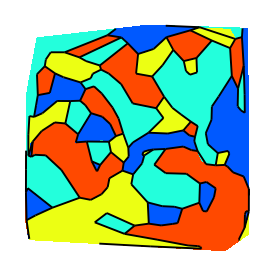
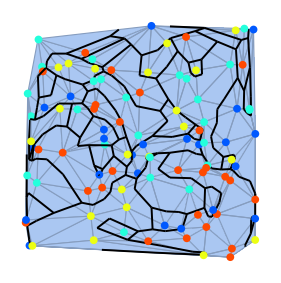

#### Visualization by material

```mathematica
ctrs=getContourAllMats2D[verts,segs,segmats,nMat,0.01];
```

```mathematica
Show[mesh,
drawPointMats2D[pts,vals,ptsize],
drawContourByMats2D[ctrs,Range[nMat],ptsize/4]
]
```

```mathematica
Manipulate[Show[
If[showMeshQ,mesh,{}],
If[showPtsQ,drawPointMats2D[pts,vals,ptsize],{}],
drawContourByMats2D[ctrs,mats,ptsize/4],
PlotRange->getRangeRatio[pts,1.1]],
{{showMeshQ,True,"Show Mesh"},{True,False}},
{{showPtsQ,True,"Show Data Points"},{True,False}},
{{mats,Range[nMat]},Range[nMat],ControlType->CheckboxBar}];
```

### Running example (3D)

```mathematica
ptsize=0.02;
```

```mathematica
n=6;
```

```mathematica
SeedRandom[0];
pts=RandomReal[{-1,1},{n,3}];
```

```mathematica
(* pts={{0,0,0},{1,0,0},{0,1,0},{0,0,1}}; *)
```

```mathematica
mesh=DelaunayMesh[pts];
HighlightMesh[mesh,{Style[0,Directive[PointSize[Medium],Black]],Style[2,Opacity[0.1]]}]
```

```mathematica
tets=Map[First,MeshCells[mesh,3]]
```

```mathematica
nMat=3;
```

```mathematica
SeedRandom[3];
vals=RandomReal[{0,1},{n,nMat}];
```

```mathematica
{verts,segs,segmats}=contourTetMultiDC[pts,tets,vals];
```

```mathematica
Show[HighlightMesh[mesh,{Style[2,Opacity[0.1]]}],
drawPointMats3D[pts,vals,0.02],
drawContour3D[verts,segs,0.02,True,True],
RotationAction->"Clip"
]
```

```mathematica
Show[HighlightMesh[mesh,{Style[2,Opacity[0.1]]}],
drawPointMats3D[pts,vals,ptsize],
drawContour3D[verts,segs,segmats,nMat,3,ptsize/2,True,True]
]
```

```mathematica
Manipulate[Show[HighlightMesh[mesh,{Style[2,Opacity[0.1]]}],
drawPointMats3D[pts,vals,ptsize],
drawContour3D[verts,segs,segmats,nMat,i,ptsize/2,showVertQ,True]
],{{i,1},1,nMat,1},{{showVertQ,False,"Show Vertices"},{True,False}}];
```

```mathematica
ctrs=getContourAllMats3D[verts,segs,segmats,nMat,0.05];
```

```mathematica
Show[HighlightMesh[mesh,{Style[2,Opacity[0.1]]}],
drawPointMats3D[pts,vals,ptsize],
drawContourByMats3D[ctrs,Range[nMat],0.7]
]
```

### Random test (3D)

#### Input

```mathematica
ptsize=0.01;
```

```mathematica
n=100;nMat=5;
```

```mathematica
SeedRandom[0];
pts=RandomReal[{-1,1},{n,3}];
(* vals=RandomReal[{0,1},{n,nMat}]; *)
centers=RandomReal[{-1,1},{nMat,3}];
vals=Map[(pt=#;Map[-Norm[pt-#]&,centers])&,pts];
```

```mathematica
mesh=DelaunayMesh[pts];
tets=Map[First,MeshCells[mesh,3]];
(* HighlightMesh[mesh,{Style[2,Opacity[0.1]]}] *)
```

#### Contouring

```mathematica
{verts,segs,segmats}=contourTetMultiDC[pts,tets,vals];
```

```mathematica
Show[
drawPointMats3D[pts,vals,0.02], 
drawContour3D[verts,segs,0.001,False,False],
RotationAction->"Clip"
]
```

```mathematica
Show[
drawPointMats3D[pts,vals,0.02], 
drawContour3DMulti[verts,segs,segmats,Table[True,{nMat}],0.001,0.9],
RotationAction->"Clip"
];
```

```mathematica
Manipulate[Show[
If[showPtsQ,drawPointMats3DDot[pts,vals,i],{}],
drawContour3D[verts,segs,segmats,nMat,i,0.01,showVertQ,showEdgeQ],PlotRange->getRangeRatio[pts,1.1]
],{{i,1},1,nMat,1},
{{showPtsQ,False,"Show Data Points"},{True,False}},{{showVertQ,False,"Show Vertices"},{True,False}},
{{showEdgeQ,False,"Show Edges"},{True,False}}];
```

#### Visualization by material

```mathematica
ctrs=getContourAllMats3D[verts,segs,segmats,nMat,0.04];
```

```mathematica
Show[(*HighlightMesh[mesh,{Style[2,Opacity[0.1]]}],*)
drawPointMats3D[pts,vals,0.02],
drawContourByMats3D[ctrs,Range[nMat],1]
]
```

```mathematica
Manipulate[Show[
If[showPtsQ,drawPointMats3D[pts,vals,0.02],{}],
drawContourByMats3D[ctrs,mats,.8],
PlotRange->getRangeRatio[pts,1.1]],
{{showPtsQ,True,"Show Data Points"},{True,False}},
{{mats,Range[nMat]},Range[nMat],ControlType->CheckboxBar}];
```